```mathematica
list={-5,-3,-1,1,3,5,7,9,11,13}
```

{-5,-3,-1,1,3,5,7,9,11,13}

```mathematica
Table[k,{k,-5,13,2}]
```

{-5,-3,-1,1,3,5,7,9,11,13}

```mathematica
Range[-5,13,2]
```

{-5,-3,-1,1,3,5,7,9,11,13}

```mathematica
Length[list]
```

10

```mathematica
list2D=Table[i+j,{i,10},{j,10}]//MatrixForm
```

(2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11
3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12
4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13
5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14
6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15
7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16
8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17
9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18
10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19
11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20)

```mathematica
Det[list2D]
```

Det[(2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11
3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12
4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13
5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14
6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15
7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16
8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17
9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18
10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19
11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20)]

```mathematica
list2D//MatrixForm
```

(2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11
3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12
4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13
5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14
6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15
7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16
8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17
9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18
10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19
11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20)

```mathematica
list2D=Table[i+j,{i,10},{j,10}]
```

{{2,3,4,5,6,7,8,9,10,11},{3,4,5,6,7,8,9,10,11,12},{4,5,6,7,8,9,10,11,12,13},{5,6,7,8,9,10,11,12,13,14},{6,7,8,9,10,11,12,13,14,15},{7,8,9,10,11,12,13,14,15,16},{8,9,10,11,12,13,14,15,16,17},{9,10,11,12,13,14,15,16,17,18},{10,11,12,13,14,15,16,17,18,19},{11,12,13,14,15,16,17,18,19,20}}

```mathematica
Det[list2D]
```

0

```mathematica
list2D//Length
```

10

```mathematica
list
```

{-5,-3,-1,1,3,5,7,9,11,13}

```mathematica
list[[5]]
```

3

```mathematica
list[[2;;5]]
```

{-3,-1,1,3}

```mathematica
list2D[[1,2]]
```

3

```mathematica
list2D[[1]][[2]]
```

3

```mathematica
list2D=Table[{i+j,i*j},{i,10},{j,10}]
```

{{{2,1},{3,2},{4,3},{5,4},{6,5},{7,6},{8,7},{9,8},{10,9},{11,10}},{{3,2},{4,4},{5,6},{6,8},{7,10},{8,12},{9,14},{10,16},{11,18},{12,20}},{{4,3},{5,6},{6,9},{7,12},{8,15},{9,18},{10,21},{11,24},{12,27},{13,30}},{{5,4},{6,8},{7,12},{8,16},{9,20},{10,24},{11,28},{12,32},{13,36},{14,40}},{{6,5},{7,10},{8,15},{9,20},{10,25},{11,30},{12,35},{13,40},{14,45},{15,50}},{{7,6},{8,12},{9,18},{10,24},{11,30},{12,36},{13,42},{14,48},{15,54},{16,60}},{{8,7},{9,14},{10,21},{11,28},{12,35},{13,42},{14,49},{15,56},{16,63},{17,70}},{{9,8},{10,16},{11,24},{12,32},{13,40},{14,48},{15,56},{16,64},{17,72},{18,80}},{{10,9},{11,18},{12,27},{13,36},{14,45},{15,54},{16,63},{17,72},{18,81},{19,90}},{{11,10},{12,20},{13,30},{14,40},{15,50},{16,60},{17,70},{18,80},{19,90},{20,100}}}

```mathematica
list2D//MatrixForm
```

((2
1) | (3
2) | (4
3) | (5
4) | (6
5) | (7
6) | (8
7) | (9
8) | (10
9) | (11
10)
(3
2) | (4
4) | (5
6) | (6
8) | (7
10) | (8
12) | (9
14) | (10
16) | (11
18) | (12
20)
(4
3) | (5
6) | (6
9) | (7
12) | (8
15) | (9
18) | (10
21) | (11
24) | (12
27) | (13
30)
(5
4) | (6
8) | (7
12) | (8
16) | (9
20) | (10
24) | (11
28) | (12
32) | (13
36) | (14
40)
(6
5) | (7
10) | (8
15) | (9
20) | (10
25) | (11
30) | (12
35) | (13
40) | (14
45) | (15
50)
(7
6) | (8
12) | (9
18) | (10
24) | (11
30) | (12
36) | (13
42) | (14
48) | (15
54) | (16
60)
(8
7) | (9
14) | (10
21) | (11
28) | (12
35) | (13
42) | (14
49) | (15
56) | (16
63) | (17
70)
(9
8) | (10
16) | (11
24) | (12
32) | (13
40) | (14
48) | (15
56) | (16
64) | (17
72) | (18
80)
(10
9) | (11
18) | (12
27) | (13
36) | (14
45) | (15
54) | (16
63) | (17
72) | (18
81) | (19
90)
(11
10) | (12
20) | (13
30) | (14
40) | (15
50) | (16
60) | (17
70) | (18
80) | (19
90) | (20
100))

```mathematica
list2D[[1]][[2]][[1]]
```

3

```mathematica
Flatten[list2D]
```

{2,1,3,2,4,3,5,4,6,5,7,6,8,7,9,8,10,9,11,10,3,2,4,4,5,6,6,8,7,10,8,12,9,14,10,16,11,18,12,20,4,3,5,6,6,9,7,12,8,15,9,18,10,21,11,24,12,27,13,30,5,4,6,8,7,12,8,16,9,20,10,24,11,28,12,32,13,36,14,40,6,5,7,10,8,15,9,20,10,25,11,30,12,35,13,40,14,45,15,50,7,6,8,12,9,18,10,24,11,30,12,36,13,42,14,48,15,54,16,60,8,7,9,14,10,21,11,28,12,35,13,42,14,49,15,56,16,63,17,70,9,8,10,16,11,24,12,32,13,40,14,48,15,56,16,64,17,72,18,80,10,9,11,18,12,27,13,36,14,45,15,54,16,63,17,72,18,81,19,90,11,10,12,20,13,30,14,40,15,50,16,60,17,70,18,80,19,90,20,100}

```mathematica
Flatten[list2D,1]
```

{{2,1},{3,2},{4,3},{5,4},{6,5},{7,6},{8,7},{9,8},{10,9},{11,10},{3,2},{4,4},{5,6},{6,8},{7,10},{8,12},{9,14},{10,16},{11,18},{12,20},{4,3},{5,6},{6,9},{7,12},{8,15},{9,18},{10,21},{11,24},{12,27},{13,30},{5,4},{6,8},{7,12},{8,16},{9,20},{10,24},{11,28},{12,32},{13,36},{14,40},{6,5},{7,10},{8,15},{9,20},{10,25},{11,30},{12,35},{13,40},{14,45},{15,50},{7,6},{8,12},{9,18},{10,24},{11,30},{12,36},{13,42},{14,48},{15,54},{16,60},{8,7},{9,14},{10,21},{11,28},{12,35},{13,42},{14,49},{15,56},{16,63},{17,70},{9,8},{10,16},{11,24},{12,32},{13,40},{14,48},{15,56},{16,64},{17,72},{18,80},{10,9},{11,18},{12,27},{13,36},{14,45},{15,54},{16,63},{17,72},{18,81},{19,90},{11,10},{12,20},{13,30},{14,40},{15,50},{16,60},{17,70},{18,80},{19,90},{20,100}}

```mathematica
list2D[[1]]
```

{{2,1},{3,2},{4,3},{5,4},{6,5},{7,6},{8,7},{9,8},{10,9},{11,10}}

```mathematica
list[[-1]]
```

13

```mathematica
list[[-2]]
```

11

```mathematica
list2D=Table[i+j,{i,10},{j,10}];
```

```mathematica
list[[2]]
```

-3

```mathematica
list2D[[2]]
```

{3,4,5,6,7,8,9,10,11,12}

```mathematica
list2D[[All,5]]
```

{6,7,8,9,10,11,12,13,14,15}

```mathematica
list2D[[6;;-1,5]]
```

{11,12,13,14,15}

```mathematica
list
```

{-5,-3,-1,1,3,5,7,9,11,13}

```mathematica
list[[3]]=10000
```

10000

```mathematica
list
```

{-5,-3,10000,1,3,5,7,9,11,13}

```mathematica
(*Add*)
Insert[list,200,8]
```

{-5,-3,10000,1,3,5,7,200,9,11,13}

```mathematica
Length[list]
```

10

```mathematica
Prepend[list,9]
```

{9,-5,-3,10000,1,3,5,7,9,11,13}

```mathematica
list
```

{-5,-3,10000,1,3,5,7,9,11,13}

```mathematica
PrependTo[list,9]
```

{9,-5,-3,10000,1,3,5,7,9,11,13}

```mathematica
list
```

{9,-5,-3,10000,1,3,5,7,9,11,13}

```mathematica
AppendTo[list,80000]
```

{9,-5,-3,10000,1,3,5,7,9,11,13,80000}

```mathematica
empty={};
```

```mathematica
AppendTo[empty,15]
```

{15}

```mathematica
Delete[list,1]
```

{-5,-3,10000,1,3,5,7,9,11,13,80000}

```mathematica
list
```

{9,-5,-3,10000,1,3,5,7,9,11,13,80000}

```mathematica
isNegative[el_]:=If[el<0,True,False]
```

```mathematica
isNegative[-100]
```

True

```mathematica
isNegative[100]
```

False

```mathematica
Select[list,isNegative]
```

{-5,-3}

```mathematica
(*Function(&)*)
```

```mathematica
Select[list,#<0&]
```

{-5,-3}

```mathematica
Select[list,Function[#<0]]
```

{-5,-3}

```mathematica
#<0&[20]
```

False

```mathematica
#<0&[-10]
```

True

```mathematica
Position[list,-5]
```

{{2}}

```mathematica
Position[list,-10]
```

{}

```mathematica
Position[list,-5][[1,1]]
```

2

```mathematica
list[[Position[list,-5]]]
```

Part::pkspec1: The expression {{2}} cannot be used as a part specification.

{9,-5,-3,10000,1,3,5,7,9,11,13,80000}⟦{{2}}⟧

```mathematica
Max[list]
```

80000

```mathematica
list[[1]]=a
```

a

```mathematica
Max[list]
```

Max[80000,a]

```mathematica
list[[1]]=-20
```

-20

```mathematica
Min[list]
```

-20

```mathematica
(*Sum List*)
```

```mathematica
Total[list]
```

90021

```mathematica
a={1.,2.,5.};b={2.,7.,0.};
```

```mathematica
a+b
```

{3,9,5}

```mathematica
α a
```

{α,2 α,5 α}

```mathematica
5 a
```

{5,10,25}

```mathematica
a.b
```

16

```mathematica
Dot[a,b]
```

16

```mathematica
Cross[a,b]
```

{-35,10,3}

```mathematica
Norm[a]
```

√30

```mathematica
Normalize[a]
```

{0.182574,0.365148,0.912871}

```mathematica
a×b
```

{-35.,10.,3.}

```mathematica
LinguisticAssistant
```

GeoPosition[{43.,25.}]

```mathematica
(*Task1*)
Table[i+2,{i,1,50}]
```

{3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52}

```mathematica
Table[2*i-1,{i,1,50}]
```

{1,3,5,7,9,11,13,15,17,19,21,23,25,27,29,31,33,35,37,39,41,43,45,47,49,51,53,55,57,59,61,63,65,67,69,71,73,75,77,79,81,83,85,87,89,91,93,95,97,99}

```mathematica
Range[1,99,2]
```

{1,3,5,7,9,11,13,15,17,19,21,23,25,27,29,31,33,35,37,39,41,43,45,47,49,51,53,55,57,59,61,63,65,67,69,71,73,75,77,79,81,83,85,87,89,91,93,95,97,99}

```mathematica
(*Task2a*)
task2a=Table[n-Sqrt[n+1]*Sqrt[n+3],{n,1,200}]//N
```

{-1.82843,-1.87298,-1.89898,-1.91608,-1.9282,-1.93725,-1.94427,-1.94987,-1.95445,-1.95826,-1.96148,-1.96424,-1.96663,-1.96872,-1.97056,-1.9722,-1.97367,-1.97498,-1.97618,-1.97726,-1.97825,-1.97916,-1.97999,-1.98076,-1.98148,-1.98214,-1.98275,-1.98333,-1.98387,-1.98437,-1.98485,-1.98529,-1.98571,-1.98611,-1.98648,-1.98684,-1.98718,-1.9875,-1.9878,-1.98809,-1.98837,-1.98863,-1.98889,-1.98913,-1.98936,-1.98958,-1.98979,-1.99,-1.9902,-1.99038,-1.99057,-1.99074,-1.99091,-1.99107,-1.99123,-1.99138,-1.99152,-1.99167,-1.9918,-1.99193,-1.99206,-1.99219,-1.99231,-1.99242,-1.99254,-1.99265,-1.99275,-1.99286,-1.99296,-1.99306,-1.99315,-1.99324,-1.99333,-1.99342,-1.99351,-1.99359,-1.99367,-1.99375,-1.99383,-1.9939,-1.99398,-1.99405,-1.99412,-1.99419,-1.99425,-1.99432,-1.99438,-1.99444,-1.99451,-1.99457,-1.99462,-1.99468,-1.99474,-1.99479,-1.99485,-1.9949,-1.99495,-1.995,-1.99505,-1.9951,-1.99515,-1.99519,-1.99524,-1.99528,-1.99533,-1.99537,-1.99541,-1.99545,-1.9955,-1.99554,-1.99558,-1.99561,-1.99565,-1.99569,-1.99573,-1.99576,-1.9958,-1.99583,-1.99587,-1.9959,-1.99593,-1.99597,-1.996,-1.99603,-1.99606,-1.99609,-1.99612,-1.99615,-1.99618,-1.99621,-1.99624,-1.99627,-1.9963,-1.99632,-1.99635,-1.99638,-1.9964,-1.99643,-1.99645,-1.99648,-1.9965,-1.99653,-1.99655,-1.99658,-1.9966,-1.99662,-1.99664,-1.99667,-1.99669,-1.99671,-1.99673,-1.99675,-1.99677,-1.99679,-1.99682,-1.99684,-1.99686,-1.99687,-1.99689,-1.99691,-1.99693,-1.99695,-1.99697,-1.99699,-1.99701,-1.99702,-1.99704,-1.99706,-1.99708,-1.99709,-1.99711,-1.99713,-1.99714,-1.99716,-1.99718,-1.99719,-1.99721,-1.99722,-1.99724,-1.99725,-1.99727,-1.99728,-1.9973,-1.99731,-1.99733,-1.99734,-1.99735,-1.99737,-1.99738,-1.9974,-1.99741,-1.99742,-1.99744,-1.99745,-1.99746,-1.99747,-1.99749,-1.9975,-1.99751,-1.99752}

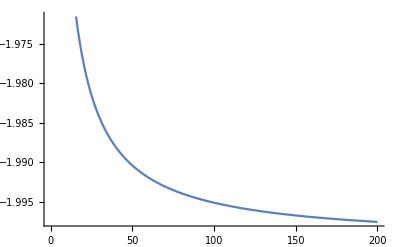

```mathematica
ListLinePlot[task2a]
```

```mathematica
(*Task2b*)
task2b=Table[((-1)^(n+1)*n)/(n+√n),{n,1,200}]//N
```

{0.5,-0.585786,0.633975,-0.666667,0.690983,-0.710102,0.725708,-0.738796,0.75,-0.759747,0.768338,-0.775991,0.782871,-0.789103,0.794787,-0.8,0.804806,-0.809256,0.813395,-0.817256,0.820871,-0.824266,0.827462,-0.830479,0.833333,-0.836039,0.83861,-0.841055,0.843387,-0.845613,0.847741,-0.849779,0.851732,-0.853608,0.855409,-0.857143,0.858812,-0.860421,0.861974,-0.863473,0.864922,-0.866323,0.86768,-0.868994,0.870268,-0.871504,0.872703,-0.873868,0.875,-0.876101,0.877171,-0.878214,0.879229,-0.880218,0.881182,-0.882122,0.883039,-0.883934,0.884808,-0.885662,0.886496,-0.887311,0.888109,-0.888889,0.889652,-0.890399,0.891131,-0.891848,0.89255,-0.893238,0.893912,-0.894574,0.895222,-0.895859,0.896483,-0.897096,0.897698,-0.898289,0.898869,-0.89944,0.9,-0.900551,0.901092,-0.901625,0.902148,-0.902663,0.90317,-0.903669,0.904159,-0.904642,0.905118,-0.905586,0.906047,-0.906502,0.906949,-0.90739,0.907824,-0.908253,0.908675,-0.909091,0.909501,-0.909906,0.910305,-0.910699,0.911087,-0.91147,0.911848,-0.912221,0.91259,-0.912953,0.913312,-0.913667,0.914017,-0.914362,0.914703,-0.915041,0.915374,-0.915703,0.916028,-0.916349,0.916667,-0.91698,0.917291,-0.917597,0.9179,-0.9182,0.918497,-0.91879,0.91908,-0.919366,0.91965,-0.91993,0.920208,-0.920482,0.920754,-0.921023,0.921289,-0.921552,0.921813,-0.922071,0.922326,-0.922579,0.922829,-0.923077,0.923322,-0.923565,0.923806,-0.924044,0.92428,-0.924514,0.924745,-0.924975,0.925202,-0.925427,0.92565,-0.925871,0.92609,-0.926307,0.926522,-0.926735,0.926946,-0.927156,0.927363,-0.927569,0.927773,-0.927975,0.928176,-0.928374,0.928571,-0.928767,0.928961,-0.929153,0.929343,-0.929532,0.92972,-0.929906,0.93009,-0.930273,0.930455,-0.930635,0.930813,-0.93099,0.931166,-0.931341,0.931514,-0.931686,0.931856,-0.932025,0.932193,-0.93236,0.932525,-0.932689,0.932852,-0.933014,0.933174,-0.933333,0.933491,-0.933648,0.933804,-0.933959}

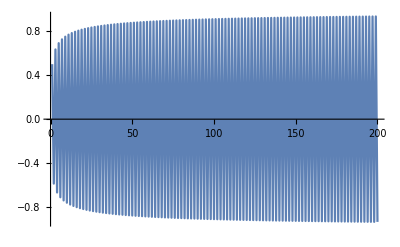

```mathematica
ListLinePlot[task2b]
```

```mathematica
(*Task2c*)
task2c=Table[Cos[n]/(1.01)^n,{n,1,500}]//N
```

{0.534953,-0.407947,-0.960877,-0.628139,0.269895,0.904524,0.703178,-0.134367,-0.833083,-0.759601,0.00396686,0.748878,0.79734,0.118956,-0.654357,-0.816712,-0.232342,0.552036,0.81839,0.334441,-0.444444,-0.803365,-0.423838,0.334069,0.772909,0.499453,-0.223312,-0.728534,-0.560551,0.114443,0.671949,0.606734,-0.00956063,-0.605008,-0.637929,-0.089437,0.52967,0.654372,0.180882,-0.447951,-0.656584,-0.263358,0.361878,0.645344,0.33571,-0.273451,-0.621661,-0.397056,0.1846,0.586737,0.446791,-0.097152,-0.541931,-0.484577,0.0128009,0.488725,0.51034,0.0669213,-0.428685,-0.524255,-0.140665,0.363427,0.526726,0.207281,-0.294576,-0.518366,-0.26583,0.223738,0.499971,0.315592,-0.152466,-0.472498,-0.356067,0.0822304,0.437029,0.38697,-0.0143968,-0.394748,-0.40823,-0.0497977,0.346908,0.419975,0.109261,-0.294801,-0.422517,-0.163062,0.239731,0.416339,0.210435,-0.182989,-0.40207,-0.250793,0.125823,0.38047,0.283724,-0.0694157,-0.352401,-0.308988,0.0148694,0.318809,0.326519,0.0368173,-0.280694,-0.336408,-0.0847616,0.239093,0.338898,0.128207,-0.195051,-0.334367,-0.166534,0.149603,0.323314,0.19926,-0.103754,-0.306341,-0.226046,0.0584571,0.284135,0.246693,-0.0145988,-0.257451,-0.261137,-0.0270138,0.22709,0.269446,0.0656667,-0.19388,-0.271806,-0.100747,0.15866,0.268513,0.13175,-0.122263,-0.259963,-0.158283,0.0854935,0.246634,0.180066,-0.0491206,-0.229072,-0.196933,0.013859,0.207881,0.208827,0.0196403,-0.183699,-0.215794,-0.0507997,0.157191,0.217978,0.0791224,-0.129029,-0.215613,-0.104198,0.0998821,0.209009,0.125706,-0.0703972,-0.198548,-0.143417,0.0411927,0.184664,0.157192,-0.0128448,-0.167837,-0.166978,-0.0141208,0.14858,0.172809,0.039237,-0.127424,-0.174796,-0.0621015,0.104909,0.17312,0.0823808,-0.0815697,-0.168029,-0.0998132,0.0579279,0.159824,0.11421,-0.0344808,-0.148851,-0.125455,0.011693,0.135493,0.133502,0.0100115,-0.120161,-0.138375,-0.0302549,0.103278,0.140157,0.0487112,-0.0852787,-0.138992,-0.0651095,0.0665919,0.135074,0.0792362,-0.0476369,-0.128642,-0.0909364,0.0288137,0.119973,0.100113,-0.0104968,-0.109371,-0.106727,-0.00697153,0.0971652,0.110792,0.0232861,-0.0836948,-0.112373,-0.0381826,0.0693069,0.111582,0.051441,-0.0543464,-0.108573,-0.0628872,0.0391503,0.103535,0.072394,-0.0240404,-0.0966885,-0.0798808,0.00931837,0.0882766,0.0853129,0.00473952,-0.0785611,-0.0886991,-0.0178865,0.0678145,0.0900892,0.0299086,-0.0563146,-0.0895706,-0.0406271,0.0443386,0.0872647,0.0499,-0.0321569,-0.0833217,-0.057623,0.0200287,0.0779164,0.0637292,-0.00819697,-0.0712434,-0.0681883,-0.00311538,0.0635116,0.0710054,0.0137089,-0.0549391,-0.0722184,-0.0234103,0.0457486,0.0718957,0.0320744,-0.0361624,-0.0701328,-0.0395856,0.0263981,0.0670491,0.0458583,-0.0166639,-0.0627835,-0.0508368,0.00715581,0.0574912,0.0544953,0.00194647,-0.051339,-0.056836,-0.0104817,0.0445017,0.0578878,0.0183096,-0.0371576,-0.0577039,-0.0253124,0.0294851,0.0563599,0.0313956,-0.021659,-0.0539501,-0.0364893,0.013847,0.0505853,0.0405473,-0.00620676,-0.046389,-0.0435474,-0.00111664,0.0414947,0.04549,0.00799296,-0.036042,-0.046397,-0.0143086,0.0301739,0.0463099,0.0199678,-0.0240337,-0.0452882,-0.0248939,0.0177617,0.0434067,0.0290294,-0.0114927,-0.0407535,-0.0323362,0.0053539,0.0374272,0.0347951,0.000537802,-0.0335341,-0.0364056,-0.00607714,0.0291863,0.037184,0.0111721,-0.0244982,-0.0371627,-0.0157451,0.0195847,0.0363886,0.0197336,-0.0145585,-0.034921,-0.0230906,0.00952822,0.0328299,0.0257844,-0.00459614,-0.0301938,-0.0277989,-0.000143371,0.0270978,0.0291326,0.00460529,-0.0236313,-0.0297979,-0.00871518,0.0198863,0.0298199,0.01241,-0.0159548,-0.0292356,-0.0156389,0.0119274,0.028092,0.0183634,-0.00789135,-0.0264445,-0.0205573,0.0039291,0.024356,0.022207,-0.000116763,-0.0218943,-0.0233104,-0.003477,0.019131,0.0238769,0.00679194,-0.0161397,-0.023926,-0.00977694,0.0129942,0.0234869,0.0123906,-0.00976734,-0.0225966,-0.0146013,0.00652931,0.0212993,0.0163876,-0.00334645,-0.0196451,-0.0177379,0.000280145,0.0176881,0.01865,0.00261414,-0.0154856,-0.0191308,-0.00528764,0.0130966,0.0191955,0.0076989,-0.0105802,-0.018867,-0.0098142,0.00799501,0.0181747,0.0116078,-0.0053974,-0.0171538,-0.0130618,0.00284082,0.0158439,0.0141666,-0.000374753,-0.0142884,-0.0149199,-0.00195599,0.0125332,0.0153268,0.00411197,-0.0106254,-0.0153991,-0.00605957,0.0086125,0.0151547,0.00777133,-0.00654153,-0.014617,-0.0092262,0.00445785,0.0138139,0.0104095,-0.00240447,-0.012777,-0.0113131,0.000421309,0.0115409,0.0119347,0.00145547,-0.0101423,-0.0122781,-0.00319395,0.00861896,0.0123525,0.00476686,-0.007009,-0.0121719,-0.00615189,0.00535013,0.0117548,0.00733183,-0.00367883,-0.0111234,-0.0082946,0.00202975,0.0103028,0.00903328,-0.000435046,-0.00932074,-0.00954584,-0.00107606,0.00820647,0.009835,0.00247776,-0.00699025,-0.00990784,-0.00374794,0.00570267,0.00977541,0.00486846,-0.00437401,-0.00945231,-0.00582525,0.00303359,0.00895613,0.00660839,-0.0017093,-0.00830697,-0.00721206,0.00042707,0.00752687,0.00763439,0.000789511,-0.00663926,-0.00787734,-0.00191956,0.00566837,0.00794636,0.00294518,-0.00463873,-0.00785014,-0.00385159,0.00357463,0.00760021,0.00462731,-0.00249967,-0.00721055,-0.00526419,0.00143629,0.00669715,0.00575734,-0.000405387,-0.00607762,-0.00610508}

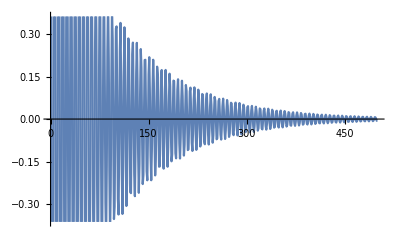

```mathematica
ListLinePlot[task2c]
```

```mathematica
task2c=Table[Cos[n]/(1.01)^n,{n,1,1000}]//N;
```

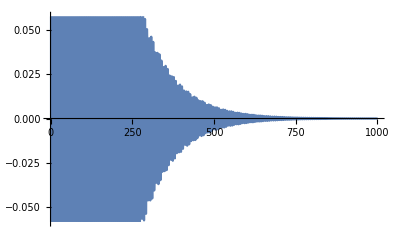

```mathematica
ListLinePlot[task2c]
```

```mathematica
Import["D:\\FMI\\Bachelor\\Informatics\\Elective Courses\\Софтуер за Научни Изчисления\\2019 - Wolfram\\Practice\\EU_visitors_oct2019.csv"]//TableForm
```

Country | Total | Holiday | Business | Other
Austria | 12818 | 3770 | 4222 | 4826
Belgium | 7250 | 1195 | 2983 | 3072
Croatia | 4040 | 817 | 1271 | 1952
Cyprus | 1476 | 518 | 589 | 369
Czech Rep. | 2601 | 756 | 1304 | 541
Denmark | 2131 | 729 | 746 | 656
Finland | 2104 | 1073 | 1031 | 0
France | 9570 | 5445 | 1650 | 2475
Germany | 39067 | 14156 | 10008 | 14903
Greece | 99743 | 15249 | 26180 | 58314
Hungary | 5563 | 2919 | 1511 | 1133
Ireland | 1107 | 507 | 600 | 0
Italy | 11147 | 3454 | 3297 | 4396
Malta | 202 | 125 | 0 | 77
Netherlands | 7431 | 2798 | 1775 | 2858
Poland | 13563 | 7583 | 4693 | 1287
Portugal | 1360 | 680 | 208 | 472
Romania | 144759 | 18739 | 30174 | 95846
Slovakia | 2047 | 607 | 510 | 930
Slovenia | 956 | 430 | 126 | 400
Spain | 4782 | 1435 | 2215 | 1132
Sweden | 2516 | 899 | 662 | 955
United Kingdom | 21268 | 8622 | 7631 | 5015

```mathematica
task3=Import["D:\\FMI\\Bachelor\\Informatics\\Elective Courses\\Софтуер за Научни Изчисления\\2019 - Wolfram\\Practice\\EU_visitors_oct2019.csv"];
```

```mathematica
task3[[All,2]]
```

{Total,12818,7250,4040,1476,2601,2131,2104,9570,39067,99743,5563,1107,11147,202,7431,13563,1360,144759,2047,956,4782,2516,21268}

```mathematica
Max[task3[[2;;,2]]]
```

144759

```mathematica
Max[task3[[2;;,4]]]
```

30174

```mathematica
Max[task3[[2;;,3]]]
```

18739

```mathematica
Select[task3,#[[2]]==144759&][[1]]
```

{Romania,144759,18739,30174,95846}

```mathematica
Select[task3,#[[4]]==30174&][[1]]
```

{Romania,144759,18739,30174,95846}

```mathematica
Select[task3,#[[3]]==18739&][[1]]
```

{Romania,144759,18739,30174,95846}